```mathematica
Import["C:\\Users\\ASUS\\Documents\\TestDATA_evShiftedHQ.dat","Table"]
```

```mathematica
e=Flatten@{{-1.3373203592411151},{-0.18643394354763032},{-0.07105746396493018},{-0.0374071689315123},{-0.023050971893692207},{-0.01561839010970445},{-0.011277794810933273},{-0.008524333099639847},{-0.006668809747345961},{-0.005359292725220399},{-0.004400800927001569},{-0.0036782198975480185},{-0.0031200305071230616},{-0.002679897830738298},{-0.002326732427661682},{-0.0020390440573301305},{-0.0018015927229981799},{-0.0016033276090361426},{-0.0014360775387558533},{-0.0012936952585533845}}
```

{-1.33732,-0.186434,-0.0710575,-0.0374072,-0.023051,-0.0156184,-0.0112778,-0.00852433,-0.00666881,-0.00535929,-0.0044008,-0.00367822,-0.00312003,-0.0026799,-0.00232673,-0.00203904,-0.00180159,-0.00160333,-0.00143608,-0.0012937}

```mathematica
Get["C:\\Users\\ASUS\\Documents\\TestDump_efHQ.mx"]
```

```mathematica
V[r_]=-(1/r)-(1.0415223038416566 E^(-0.9990999998788636 r))/r;α=2.;
```

```mathematica
sol=With[{r1=2000,r2=1.*10^-10},ParametricNDSolve[{V[r] f[r]-1/α f''[r]==en f[r],f[r1]==r2,f'[r1]==-r2},f,{r,0,r2},en,WorkingPrecision->80,MaxSteps->Infinity,AccuracyGoal->20,MaxStepFraction->10^-3,Method->"StiffnessSwitching"]]
```

{f→ParametricFunction[<>]}

```mathematica
ensol=FindRoot[f[en][1.*10^-10]==0/.sol,{en,-0.0374},WorkingPrecision->50,AccuracyGoal->20]
```

ParametricNDSolve::ndsz: 在 r == 1.6981164786718320282544348333408233692879313254237424496368138629974179690831949×10^-76 处，步长实际上为零；可能存在奇点或者刚性系统.

Power::infy: 碰到无穷表达式 1/0.

Infinity::indet: 碰到不定表达式 ComplexInfinity+ComplexInfinity.

ParametricNDSolve::nlnum: 在 {r$324,f[r$324],f'[r$324],en$323} = {0,-1.9703999385652122831574121733527535543325772752908361995547464948669316020000517×10^-11,-3.1653527292191290496996866753340852363149815779170321617539333423312366027622495×10^-9,10.336600000000000676436684443615376949310302734375} 处，函数值 {-3.1653527292191290496996866753340852363149815779170321617539333423312366027622495×10^-9,Indeterminate} 不是由数字组成的维度为 {2} 的列表.

Power::infy: 碰到无穷表达式 1/0.

Infinity::indet: 碰到不定表达式 ComplexInfinity+ComplexInfinity.

ParametricNDSolve::nlnum: 在 {r$324,f[r$324],f'[r$324],en$323} = {0,-1.9703999385652122831574121733527535543325772752908361995547464948669316020000517×10^-11,-3.1653527292191290496996866753340852363149815779170321617539333423312366027622495×10^-9,10.336600000000000676436684443615376949310302734375} 处，函数值 {-3.1653527292191290496996866753340852363149815779170321617539333423312366027622495×10^-9,Indeterminate} 不是由数字组成的维度为 {2} 的列表.

Experimental`NumericalFunction::nlnum1: 当参数为 {0,{-1.9703999385652122831574121733527535543325772752908361995547464948669316020000517×10^-11,-3.1653527292191290496996866753340852363149815779170321617539333423312366027622495×10^-9},{«55»},{{1.9703999548215197564502858700312612080325455030015487211789939533638358374318593×10^-31},{-3.9407998953182091325384564589262988871220455828269027072941504791085577297672869×10^-21}}} 时，函数值 {«1»[Jacobian[0,{-1.9703999385652122831574121733527535543325772752908361995547464948669316020000517×10^-11,-3.1653527292191290496996866753340852363149815779170321617539333423312366027622495×10^-9},{10.336600000000000676436684443615376949310302734375},InputIndex→2]].{{1.9703999548215197564502858700312612080325455030015487211789939533638358374318593×10^-31},{-«90»}},«90»+«1»} 不是由数字组成的维度为 {2} 的列表.

Experimental`NumericalFunction::nlnum1: 当参数为 {0,{-1.9703999385652122831574121733527535543325772752908361995547464948669316020000517×10^-11,-3.1653527292191290496996866753340852363149815779170321617539333423312366027622495×10^-9},{{1.9703999548215197564502858700312612080325455030015487211789939533638358374318593×10^-31},{-«90»}},{10.336600000000000676436684443615376949310302734375}} 时，函数值 {Experimental`NumericalFunction[{Function[{r$324,f,NDSolve`f$2$1,en$323},{NDSolve`f$2$1,-2. (Times[«2»]+Times[«3»])}],Apply},«4»,{Function[{NDSolve`Monitor$1900},Function[{NDSolve`Monitor$1900$1901,NDSolve`Monitor$1900$1902,NDSolve`Monitor$1900$1903,en$323},Internal`InheritedBlock[{Derivative,f,r$324},«1»=.;«1»=.;«1»=.;Set[«2»];Set[«2»];Set[«2»];NDSolve`Monitor$1900]]],None,None}][«1»],«1»} 不是由数字组成的维度为 {4} 的列表.

Power::infy: 碰到无穷表达式 1/0.

General::stop: 在本次计算中，Power::infy 的进一步输出将被抑制.

Infinity::indet: 碰到不定表达式 ComplexInfinity+ComplexInfinity.

General::stop: 在本次计算中，Infinity::indet 的进一步输出将被抑制.

ParametricNDSolve::nlnum: 在 {r$324,f[r$324],f'[r$324],en$323} = {0,5.9859595448692362578195908179643245142677027386898582949100998325152461808944077×10^-11,5.8702826838356992253953048711838091079165906666524571756674969503432107553657693×10^-9,123.70260000000001809894456528127193450927734375} 处，函数值 {5.8702826838356992253953048711838091079165906666524571756674969503432107553657693×10^-9,Indeterminate} 不是由数字组成的维度为 {2} 的列表.

General::stop: 在本次计算中，ParametricNDSolve::nlnum 的进一步输出将被抑制.

Experimental`NumericalFunction::nlnum1: 当参数为 {0,{5.9859595448692362578195908179643245142677027386898582949100998325152461808944077×10^-11,5.8702826838356992253953048711838091079165906666524571756674969503432107553657693×10^-9},{«52»},{{-5.9859595683723440813260044207206793841831706454861879185611829058546018586360233×10^-31},{1.197191910480322542450538374251482374444792753141658931798992716318908755388687×10^-20}}} 时，函数值 «1» 不是由数字组成的维度为 {2} 的列表.

General::stop: 在本次计算中，Experimental`NumericalFunction::nlnum1 的进一步输出将被抑制.

$Aborted

```mathematica
ensol
```

{en→-0.037407168817952223799594754916581669109773570996048002405878578673356618361772709}

NDSolve::precw: 参数函数的精度 ({{(-Power[«2»]-1.04152 Power[«2»] Power[«2»]) f[r]-0.5 f''[r]==-0.0374072 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) 小于 WorkingPrecision (80.).

Power::infy: 碰到无穷表达式 1/0.

Infinity::indet: 碰到不定表达式 ComplexInfinity+ComplexInfinity.

NDSolve::nlnum: 在 {r,f[r],f'[r]} = {0,-5.0610839850810836225504920333636788457503540749728380714945265645895657125790359×10^160,-8.1751084972484147781878307449260393227671043784891721020802671125158232612914282×10^177} 处，函数值 {-8.1751084972484147781878307449260393227671043784891721020802671125158232612914282×10^177,Indeterminate} 不是由数字组成的维度为 {2} 的列表.

NDSolve::nderr: 在 r == 0.0050710969006527348391902311746690647002633329365325264051640276095429552296905157 处误差测试失败；无法继续.

-5.00064×10^-179

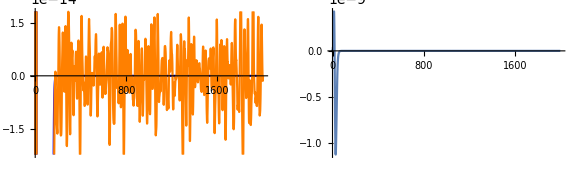

```mathematica
enf4=Flatten@With[{r1=2000,r2=1.*10^-50},NDSolve[{V[r] f[r]-1/α f''[r]==(*(en/.ensol)*)-0.037407168817952221(*e[[4]] *)f[r],f[r1]==r2,f'[r1]==-r2},f,{r,r1,0},WorkingPrecision->80,AccuracyGoal->20,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepSize->0.01,Method->{"Shooting","StartingInitialConditions"->{f'[r2]==1,f[r2]==r2}}]];
am4=((f[2]/.enf4)/(ef[[4]][2]))^-1
GraphicsGrid[{{Plot[{am4 f[r]/.enf4,ef[[4]][r]},{r,0,2000},PlotStyle->{Blue,Orange}],Plot[(am4 f[r]/.enf4)-ef[[4]][r],{r,0,2000},PlotRange->Full]}},ImageSize->Large]
```

InterpolatingFunction::dmval: 输入值 {0.00102143} 位于插值函数的数据范围之外. 将使用外推法.

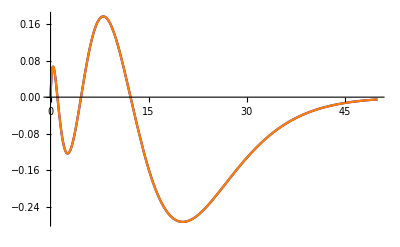

```mathematica
Plot[{am4 f[r]/.enf4,ef[[4]][r]},{r,0,50},PlotStyle->{Blue,Orange},PlotRange->All]
```

```mathematica
f[r]/.enf4/.r->0
```

8.1750868532007043056193583586616077982610811761740112370643706868593216796018154×10^167

```mathematica
Plot[f[r]/.enf4,{r,0,100}]
```

-Graphics-

```mathematica
NIntegrate[am4^2 D[f[r]/.enf4,{r,2}]^2,{r,1.*10^-50,2000},MaxRecursion->20]
```

2.78627×10^30

```mathematica
am4^2 NIntegrate[(f[r]/r^3)^2/.enf4,{r,1.*10^-10,2000},MaxRecursion->20,WorkingPrecision->100]
```

NIntegrate::ncvb: 在接近 {r} = {2.72967509619926384756214668208957103491518122494262794952786631704952113911387527597421813206554448617497688307550859210695285372975102456211658608384×10^-10} 处的 r 中进行 20 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 2.22776352427026075027567439455047707351325744681929261903896777262782880474497639650474509599387665881572099443348137130292442266975920834247067393712×10^384 和 5.1610518044893889125678296675435819202419846907941991656016595719346837859544192295114137394061383189608672429356770843857282253132602766656575368268×10^358.

5.57084444772795×10^27

```mathematica
NIntegrate[D[ef[[4]][r]/.enf4,{r,2}]^2,{r,0,2000}]
```

NIntegrate::ncvb: 在接近 {r} = {0.558842} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.53347 和 0.000605224.

0.53347